```mathematica
v0={10,3};
GG=9.81;
H=10;
X[t_]:=Expand[{0,H}+v0*t+({0,-GG}*t^2)/2]
```

X0={0,H}, a={0,-GG}

```mathematica
X[2]
```

{20,-3.62}

```mathematica
v[t_]:=v0+{0,-GG}*t
```

```mathematica
v[3]
```

{10,-26.43}

```mathematica
SlikaTocke[t_]:=Point[X[t]]
```

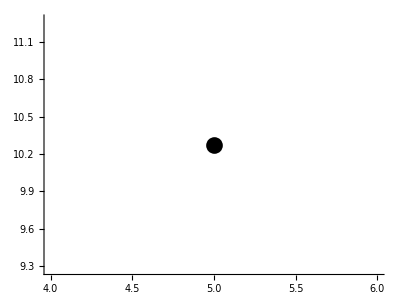

```mathematica
Graphics[{PointSize[0.03],SlikaTocke[0.5]},{Axes->True,AspectRatio->Automatic}]
```

```mathematica
PremikVektorja[t_]:={Arrowheads[Large],Arrow[{X[t],X[t]+v[t]}]}
```

```mathematica
PremikVektorja[3]
```

{Arrowheads[Large],Arrow[{{{30,-25.145}},{40,-51.575}}]}

```mathematica
SlikaVektorja[t_]:=Graphics[{PointSize[0.02],SlikaTocke[t],PremikVektorja[t]},Axes->True,PlotRange->{{-1,25},{-5,15}}]
```

```mathematica
Manipulate[{SlikaVektorja[t]},{t,0,0.3058103975535168}]
```

```mathematica
Cas=Solve[v[t][[2]]==0,t]
```

{{t→0.30581}}

```mathematica
X[Flatten[Cas]]
```

Thread::tdlen: Objects of unequal length in {10,3} {t→0.30581} cannot be combined.

Thread::tdlen: Objects of unequal length in 1/2 {0,-9.81} {(t→0.30581)^2} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{1/2 {(t→0.30581)^2} {0,-9.81}+{t→0.30581} {10,3},10+1/2 {(t→0.30581)^2} {0,-9.81}+{t→0.30581} {10,3}}